# Poisson Summation Formula trick

## Taboo Transition density for t ϵ [(n-1)/n,1]

### Fourier transform

```mathematica
f[y_]:=(1-Exp[-2n(g2-y)(g1-x)])PDF[NormalDistribution[0,1/(√n)],y-x]If[y<g2,1,0]
```

Change of variable, centering the transition probability in terms of distance from the boundary

```mathematica
f[g2+x]
```

(ⅇ^(-(g2^2 n)/2) (1-ⅇ^(2 n (g1-x) x)) √n If[g2+x<g2,1,0])/(√(2 π))

Shifted boundary lying θ away from the boundary. z ϵ [0,∞). θ ϵ [0,h]. This is a change of variable g_2-y maps to z + θ

```mathematica
f3[z_]:=(1-Exp[-2n( z+θ)(g1-x)])PDF[NormalDistribution[0,1/(√n)],g2-(z+ θ)-x]If[z+ θ>0,1,0]
```

Fourier transform of f_(n,x,θ)

```mathematica
Timing[FullSimplify[Assuming[n>0 &&g1>0 && g2>0 && Element[g1, Reals] && Element[g2, Reals]&& Element[x, Reals] && Element[n, Reals] && Element[s, Reals],FourierTransform[f3[y],y,s,FourierParameters->{0,-2Pi}]],n>0 &&g1>0 && g2>0 && Element[g1, Reals] && Element[g2, Reals]&& Element[x, Reals] && Element[n, Reals] && Element[s, Reals]]]
```

{24.9688,1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))}

```mathematica
fhat[s_]:=1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))
```

There appears to be gain from analysing only the real part.

```mathematica
Manipulate[
ListLogLogPlot[{
Table[Abs[Re[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)])) ]],{s,1,20,1}],
Table[Abs[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))] ,{s,1,20,1}]

}, PlotRange->Full,PlotLegends->{ "Real FT","Abs FT"}],{{x,0},-3,g1},{{g1,0.6},0.5,3},{{g2,0.6},0.5,3},{θ,0,1},{{n,3},3,20,1}]
```

### Asymptotic expansions

Using two expansions: 1. erf(z) ~ Exp[-z^2]/(√π z) and 2. erfz(-z)-2 ~ (-Exp[-z^2])/(√π z). These expansions are only valid for |Ph[z]|  <(3π)/2.   Let z_1= (n(x-g_2)+2π ⅈ s)/(√(2n)), z_2=(n(g_2-2 g_1+x )- 2π ⅈ s)/(√(2n)). Let z_1^*=-z_1= (n(g_2-x)-2π ⅈ s)/(√(2n))and z_2^*=-z_2=(n(2 g_1-g_2-x)+2π ⅈ s)/(√(2n)). Both the real parts of z_1^*and z_2^* ensure that |Ph[z]|  <(3π)/2

```mathematica
{Series[Erfc[-z],{z,∞,1}],Series[-2+ Erfc[-z],{z,∞,1}]}
```

{2+ⅇ^(-z^2) (-1/(√π z)+O[1/z]^2),ⅇ^(-z^2) (-1/(√π z)+O[1/z]^2)}

Hence we replace Erfc[z_1] = Erfc[-z_1^*] ~ 2 - Exp[-z_1^(*2)]/(√π z_1^*)=2 + Exp[-z_1^2]/(√π z_1) and -2 + Erfc[z_2] = -2 + Erfc[-z_2^*] ~ Exp[-z_2^(*2)]/(√π(-z_2^*))=Exp[-z_2^2]/(√π z_2)

```mathematica
z1 := (n (x-g2)+2 ⅈ π s)/(√(2n))
```

```mathematica
z2:= (n (-2 g1+g2+x)-2 ⅈ π s)/(√(2 n))
```

The error of these expansions is bounded above by |(ⅇ^(-z^2))/(√π z^3)|(see eqn 2.09 and 2.10 of Asymptotics and special functions [Olver]). We bound this above by |(ⅇ^(-z^2))/(√π z)|, and so we get two times the error - we need to be careful here we absolute value signs. The error explodes when θ = π/2, which corresponds to Re(z) = 0, i.e. x = g_1. Factorising the expansions yields a (g-x), which causes both the difference bewteen the erfc and also the asymptotic exapansions to go to zero.

```mathematica
Manipulate[LogPlot[{Abs[Erfc[a ⅇ^(ⅈ θ)]-(ⅇ^(-(a ⅇ^(ⅈ θ))^2))/(√π a ⅇ^(ⅈ θ))],Abs[(ⅇ^(-(a ⅇ^(ⅈ θ))^2))/(√π a ⅇ^(ⅈ θ))]},{θ,-π,π},PlotLegends->{"Expansion error", "First term"}, PlotLabel->"Erfc expansion error"],{a,1,30}]
```

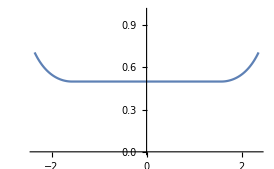

```mathematica
Plot[If[x≤ π/2&& x > -π/2 ,1/2,0]+If[x > π/2|| x<-π/2,1,0] 1/(2Abs[Sin[x]]),{x,(-3π)/4,(3π)/4},PlotRange->{{(-3π)/4,(3π)/4},{0,1}}]
```

One of the terms becomes (2n)/((n^2(g2 - x))^2+4 π^2 s^2)

```mathematica
1/ComplexExpand[Abs[z1^2]] // Factor
```

(2 √(n^2))/(g2^2 n^2+4 π^2 s^2-2 g2 n^2 x+n^2 x^2)

The multiplier error from the first expansion is

```mathematica
ComplexExpand[Abs[ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n)ⅇ^(4 ⅈ π s x+2 g1 n (g2+x))]]
```

ⅇ^(-(2 π^2 s^2)/n)

Looking at the second term, which is slightly more annoying. (n^2(x + g_2- 2 g_1))^2+4 π^2 s^2

```mathematica
Expand[n^2(x + g2 - 2g1)^2]
```

4 g1^2 n^2-4 g1 g2 n^2+g2^2 n^2-4 g1 n^2 x+2 g2 n^2 x+n^2 x^2

```mathematica
1/ComplexExpand[Abs[z2^2]] //Factor
```

(2 √(n^2))/(4 g1^2 n^2-4 g1 g2 n^2+g2^2 n^2+4 π^2 s^2-4 g1 n^2 x+2 g2 n^2 x+n^2 x^2)

The multiplier is no longer so simple, and has dependence on x. Simplifying gives Exp( 2n g_1(g_1-g_2)  )Exp[-2 π^2 s^2/n]Exp[2nx(g2  - g1)]

```mathematica
ComplexExpand[Abs[ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n)ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x)]]
```

ⅇ^(2 g1^2 n-(2 π^2 s^2)/n+2 g2 n x-2 g1 n (g2+x))

We see that the integral is bounded uniformly in n

```mathematica
∫_(-∞)^g1 (g1-x)PDF[NormalDistribution[0,1],x] ⅇ^(2 n x(g2-g1))ⅆx
```

1/2 ⅇ^(-1/2 g1 (g1+4 g1 n-4 g2 n)) (√(2/π)+ⅇ^(1/2 (g1+2 g1 n-2 g2 n)^2) (g1+2 g1 n-2 g2 n) (1+Erf[(g1+2 g1 n-2 g2 n)/(√2)]))

### Substitution of asymptotic expansions

Hence we are left with an exponentially decaying term and the EMSF error

```mathematica
1/2 ⅇ^(-2 g1 n (g2+x)-(2 (π s)^2)/n + ⅈ n (g2+x-θ))( ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) (2  +Exp[-z1^2]/(√π z1) )+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (Exp[-z2^2]/(√π z2)))
```

Looking at just the exponentials after expansion, we can factorise.

```mathematica
(ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) ( Exp[-z1^2]/(√π z1))+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (Exp[-z2^2]/(√π z2)))//Simplify
```

(2 ⅇ^(-(g2^2 n)/2+2 g1 n (g2+x)+(2 π s+ⅈ n x)^2/(2 n)+g2 (2 ⅈ π s+n x)) n^(3/2) √(2/π) (g1-x))/((2 g1 n-g2 n+2 ⅈ π s-n x) (-g2 n+2 ⅈ π s+n x))

The exponentially decaying term also is dealt with nicely

```mathematica
ⅇ^(-2 g1 n (g2+x)-(2 (π s)^2)/n + ⅈ n (g2+x-θ)) ⅇ^(4 ⅈ π s x+2 g1 n (g2+x))//Simplify
```

ⅇ^(-(2 π^2 s^2)/n+4 ⅈ π s x+ⅈ n (g2+x-θ))

Multipying the stuff in the front with the exponential terms

```mathematica
1/2 ⅇ^(-2 g1 n (g2+x)-(2 (π s)^2)/n + ⅈ n (g2+x-θ))(2 ⅇ^(-(g2^2 n)/2+2 g1 n (g2+x)+(2 π s+ⅈ n x)^2/(2 n)+g2 (2 ⅈ π s+n x)) n^(3/2) √(2/π) (g1-x))/((2 g1 n-g2 n+2 ⅈ π s-n x) (-g2 n+2 ⅈ π s+n x))//Simplify
```

-(ⅇ^(-(g2^2 n)/2+2 ⅈ π s x+g2 (2 ⅈ π s+n (ⅈ+x))-1/2 n (-2 ⅈ x+x^2+2 ⅈ θ)) n^(3/2) √(2/π) (-g1+x))/((g2 n-2 ⅈ π s-n x) (-2 g1 n+g2 n-2 ⅈ π s+n x))

Hence our error becomes

```mathematica
ⅇ^(-(2 π^2 s^2)/n+4 ⅈ π s x+ⅈ n (g2+x-θ)) -(ⅇ^(-(g2^2 n)/2+2 ⅈ π s x+g2 (2 ⅈ π s+n (ⅈ+x))-1/2 n (-2 ⅈ x+x^2+2 ⅈ θ)) n^(3/2) √(2/π) (-g1+x))/((g2 n-2 ⅈ π s-n x) (-2 g1 n+g2 n-2 ⅈ π s+n x))
```

Finding a lower bound of the absolute value of the denominator, we get 4 π^2 s^2

```mathematica
ComplexExpand[ Abs[(g2 n-2 ⅈ π s-n x) (-2 g1 n+g2 n-2 ⅈ π s+n x)]]
```

√(4 π^2 s^2+(g2 n-n x)^2) √(4 π^2 s^2+(-2 g1 n+g2 n+n x)^2)

Taking only the real part of the exponential, since we are taking absolute value of the exponential. -n/2(g_2-x)^2

```mathematica
ComplexExpand[Re[-(g2^2 n)/2+2 ⅈ π s x+g2 (2 ⅈ π s+n (ⅈ+x))-1/2 n (-2 ⅈ x+x^2+2 ⅈ θ)]]
```

-(g2^2 n)/2+g2 n x-(n x^2)/2

Hence we are left with the two major sources of error, which agrees with the EMSF. We see that boundary shifting makes no difference for the last transition.

```mathematica
ⅇ^(-(2 π^2 s^2)/n)+ (n^(3/2) √(2/π) (g1-x)ⅇ^(-n/2(g2 -x)^2))/(4 π^2 s^2)
```

### Final approximation comparison

Plot of our approximation vs true. We have multiplied by two to account for all error terms.

```mathematica
Manipulate[
LogLogPlot[{
ⅇ^(-(2 π^2 s^2)/n)+ (2 n^(3/2) √(2/π) (g1-x)ⅇ^(-n/2(g2 -x)^2))/(4 π^2 s^2)/.s-> k n^a,
Abs[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))]/.s-> k n^a /. θ-> 0
}
,{n,1,100}, PlotRange->Full, PlotLabel->"True vs Approximation", PlotLegends->{"Vin upper bound","True error"}],{x,-3,g1},{g1,0.5,3},{g2,0.5,3},{k,1,20,1},{a,0.5,1}]
```

## Taboo Transition density for t ϵ [0,(n-1)/n)

### Fourier transforms

This is the part of the taboo transition density that depends on the x_k position.

```mathematica
f2[x1_]:=(1-Exp[-2n(g2-x2)(g1-x1)])PDF[NormalDistribution[0,1/(√n)],x2-x1](1-Exp[-2n(g0-x0)(g1-x1)])PDF[NormalDistribution[0,1/(√n)],x1-x0]If[x1<g1,1,0]
```

From numerical experiments, it is clear that boundary dependent positioning is important to ensure h^4 convergence. Hence we center the density at z = g_1-x_1and then shift z by θ ϵ [0,h] from the boundary also. So x_1=g_1-z_1

```mathematica
f2θ[z_]:=(1-Exp[-2n(g2-x2)(z + θ)])PDF[NormalDistribution[0,1/(√n)],g1 - (z + θ) -x2](1-Exp[-2n(g0-x0)(z + θ)])PDF[NormalDistribution[0,1/(√n)],g1-(z+θ)-x0]If[z +θ>0,1,0]
```

```mathematica
f2[z_]:=(1-Exp[-2n(g2-x2)z])PDF[NormalDistribution[0,1/(√n)],g1 - z -x2](1-Exp[-2n(g0-x0)z ])PDF[NormalDistribution[0,1/(√n)],g1-z-x0]If[z>0,1,0]
```

Fourier transform sitting on the boundary

```mathematica
Timing[
Assuming[n>0 &&g0>0&&g1>0 && g2>0&&θ >0&& Element[θ, Reals]  && Element[g0, Reals] && Element[g1, Reals]&& Element[g2, Reals]&& Element[x0, Reals] && Element[z, Reals] && Element[x2, Reals]&& Element[n, Reals] && Element[s, Reals],
FourierTransform[f2[z],z,s,FourierParameters->{0,-2Pi}]]
]
```

{38.0469,1/(2 π)n ((ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π)/(2 √n)-(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π)/(2 √n)-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π)/(2 √n)+(ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π)/(2 √n)-(ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)])/(2 √n)-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)])/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)])/(2 √n)+(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)])/(2 √n))}

The Fourier transform isn’t too bad!

```mathematica
f2hat[s_]:=1/(2 π)n ((ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π)/(2 √n)-(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π)/(2 √n)-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π)/(2 √n)+1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π-1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)]-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)])/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)])/(2 √n)+(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)])/(2 √n))
```

Simplification allows us to factorise, and get 4 complentary error functions

```mathematica
f2hatsimp[s_]:=1/(2 π)n (1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π (1-Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)])-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]-1))/(2 √n)+(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π (1+Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)]))/(2 √n))
```

We see from the plots that taking the absolute value is too crude. We need to analyse the real part of the Fourier transform.

```mathematica
Show[
GraphicsGrid[
{
{ListLogLogPlot[
{Table[Abs[Re[f2hat[k]]] /. g1-> 1 /. g0-> 0.9 /. g2-> 1.2 /. x0-> 0.6 /. x2-> 0 /. θ->0 /. n-> 4,{k,1,30}],
Table[1/k^4,{k,1,30}]},PlotLegends->{"Re[fhat(k)]","1/k^4"},PlotLabel->"Real part only"],
ListLogLogPlot[
{Table[Abs[f2hat[k]]/. g1-> 1 /. g0-> 0.9 /. g2-> 1.2 /. x0-> 0.6 /. x2-> 0 /. θ->0.5 /. n-> 4,{k,1,30}],
Table[1/k^4,{k,1,30}]},PlotLegends->{"Abs[fhat(k)]","1/k^4"},PlotLabel->"Absolute value"]
}
}
]
]
```

```mathematica
ComplexExpand[Re[ⅇ^(a + b ⅈ)(c + ⅈ d)]]//Factor
```

ⅇ^a (c Cos[b]-d Sin[b])

### Expansion of the zk1, zk4 terms (agnostic to complex phase)

First we need to do 4 asymptotic expansions. zk_1=1/(2 √n)[n(g_0-x_0)+n(g_2-x_2)+n((g_0-g_1)+(g_2-g_1))]. zk_2=1/(2 √n)(n(g_1- ))

```mathematica
zk1 := (2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)
```

```mathematica
zk2 := (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)
```

```mathematica
zk3 :=(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)
```

```mathematica
zk4 := (2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)
```

The expansion for 1-Erf(z1)

```mathematica
(2 ⅇ^(-(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^2/(4 n)) √n)/(√π (2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2))
```

The expansion for 1+Erf(z4)

```mathematica
2-(2 ⅇ^(-(2 g1 n-2 ⅈ π s-n (x0+x2))^2/(4 n)) √n)/(√π (2 g1 n-2 ⅈ π s-n (x0+x2)))
```

Putting together the zk1 and zk4 term we get

```mathematica
1/(2 π)n (1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π (2 ⅇ^(-(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^2/(4 n)) √n)/(√π (2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2))+(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π (-(2 ⅇ^(-(2 g1 n-2 ⅈ π s-n (x0+x2))^2/(4 n)) √n)/(√π (2 g1 n-2 ⅈ π s-n (x0+x2)))))/(2 √n))//Simplify
```

(ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n (g0 n-2 g1 n+g2 n+2 ⅈ π s))/(π (-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2) (2 g1 n-2 ⅈ π s-n (x0+x2)))

It is clear that the h^4 phenomenon comes from the Real part .

```mathematica
Manipulate[
ListLogLogPlot[{
Table[Abs[Re[(ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n (g0 n-2 g1 n+g2 n+2 ⅈ π s))/(π (-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2) (2 g1 n-2 ⅈ π s-n (x0+x2)))]],{s,1,20,1}],
Table[Abs[(ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n (g0 n-2 g1 n+g2 n+2 ⅈ π s))/(π (-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2) (2 g1 n-2 ⅈ π s-n (x0+x2)))] ,{s,1,20,1}]

}, PlotRange->Full,PlotLegends->{ "Real FT","Abs FT"}],{{x0,0},-3,g0},{{x2,0},-3,g2},{{g0,0.6},0.5,3},{g1,0.5,3},{g2,0.5,3},{{n,3},3,20,1},{{a,0.75},0.5,1},{nmax,30,100}]
```

The left over decaying term form the ‘2’ is

```mathematica
1/(2 π)n ((ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π 2)/(2 √n))//Simplify
```

(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √n)/(2 √π)

### Expansion of zk2 and zk3 terms

```mathematica
zk2 := (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)
```

```mathematica
zk3 :=(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)
```

```mathematica
1/(2 π)n (-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]-1))/(2 √n))
```

It appears we need to analyse the Real part to maintain the h^4

```mathematica
Manipulate[
ListLogLogPlot[{
Table[Abs[Re[1/(2 π)n (-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]-1))/(2 √n))]],{s,1,20,1}],
Table[Abs[1/(2 π)n (-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]-1))/(2 √n))] ,{s,1,20,1}]

}, PlotRange->Full,PlotLegends->{ "Real FT","Abs FT"},PlotLabel->"(k,fhat[k])"],{{x0,0},-3,g0},{{x2,0},-3,g2},{{g0,0.6},0.5,3},{g1,0.5,3},{g2,0.5,3},{{n,3},3,20,1},{{a,0.75},0.5,1},{nmax,30,100}]
```

```mathematica
Manipulate[
ListLogLogPlot[{
Table[Abs[Re[1/(2 π)n (-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]-1))/(2 √n))]],{s,1,20,1}],
Table[Abs[Re[1/(2 π)n (-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (1-(2 ⅇ^(-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2))+(√n √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/n))/(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (-1-(2 ⅇ^(-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2))+(√n √((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/n))/(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)))/(2 √n))]],{s,1,20,1}],
Table[Abs[Re[1/(2 π)n (-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (2-(2 ⅇ^(-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2))))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (-(2 ⅇ^(-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2))))/(2 √n))]],{s,1,20,1}]

}, PlotRange->Full,PlotLegends->{ "Real FT","Asymptotic Expansion (direction independent)","Asmyp. (+∞)"},PlotLabel->"(k,fhat[k])"],{{x0,0},-3,g0},{{x2,0},-3,g2},{{g0,0.6},0.5,3},{g1,0.5,3},{g2,0.5,3},{{n,3},3,20,1},{{a,0.75},0.5,1},{nmax,30,100}]
```

```mathematica
Manipulate[
ListLogLogPlot[{
Table[Abs[Re[1/(2 π)n (-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]-1))/(2 √n))]]/. s-> k n^a,{n,1,100,1}],
Table[Abs[Re[1/(2 π)n (-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (1-(2 ⅇ^(-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2))+(√n √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/n))/(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (-1-(2 ⅇ^(-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2))+(√n √((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/n))/(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)))/(2 √n))]]/. s-> k n^a,{n,1,100,1}],
Table[Abs[Re[1/(2 π)n (-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (2-(2 ⅇ^(-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2))))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (-(2 ⅇ^(-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2))))/(2 √n))]]/. s-> k n^a,{n,1,100,1}]

}, PlotRange->Full,PlotLegends->{ "Real part","Asmyp. (|z| → ∞)","Asmyp. (z → +∞)"},PlotLabel->"(k,fhat[k])",PlotStyle->{Opacity[oa],Opacity[ob],Opacity[oc]}],{{x0,0},-3,g0},{{x2,0},-3,g2},{{g0,0.6},0.5,3},{g1,0.5,3},{g2,0.5,3},{{k,1},1,5,1},{{a,0.75},0.5,1},{{oa,0.5},0,1},{{ob,0.5},0,1},{{oc,0.5},0,1}]
```

The exponentials give rise to a similar term to the z1 and z4 terms.

```mathematica
1/(2 π)n (-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (-(2 ⅇ^(-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2))))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (-(2 ⅇ^(-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2))))/(2 √n))//Simplify
```

(ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n (g0 n-2 g1 n+g2 n+2 ⅈ π s))/(π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2) (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2))

Extracting the real part of this expression:

```mathematica
ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2)))ComplexExpand[Re[(n (g0 n-2 g1 n+g2 n+2 ⅈ π s))/(π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2) (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2))]]//Simplify
```

(ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n^2 ((2 g1-g2) (4 g1^2 n^2-4 g1 g2 n^2+4 π^2 s^2-n^2 (x0-x2) (2 g2+x0-x2))+2 g0^2 n^2 (2 g1-2 g2-x0+x2)+g0 (-12 g1^2 n^2-4 g2^2 n^2-4 π^2 s^2+n^2 x0^2+4 g1 n^2 (4 g2+x0-x2)-2 n^2 x0 x2+n^2 x2^2)))/(π (4 g0^2 n^2+4 g1^2 n^2+4 π^2 s^2+n^2 x0^2+4 g1 n^2 (x0-x2)-4 g0 n^2 (2 g1+x0-x2)-2 n^2 x0 x2+n^2 x2^2) (4 g1^2 n^2+4 g2^2 n^2+4 π^2 s^2+n^2 x0^2+4 g2 n^2 (x0-x2)-4 g1 n^2 (2 g2+x0-x2)-2 n^2 x0 x2+n^2 x2^2))

#### Left overs terms

The left over terms are completely destroyed by the exponentially fast decaying term. Real part is indistinguishable from imaginary part.

```mathematica
Manipulate[
ListLogLogPlot[{
Table[Abs[Re[1/(2 π)n (-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (1+(√n √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/n))/(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (-1+(√n √((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/n))/(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)))/(2 √n))]],{s,1,30,1}],
Table[Abs[1/(2 π)n (-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (1+(√n √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/n))/(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (-1+(√n √((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/n))/(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)))/(2 √n))],{s,1,30,1}]

}, PlotRange->Full,PlotLegends->{ "Real part","Abs part"},PlotLabel->"(k,fhat[k])",PlotStyle->{Opacity[oa],Opacity[ob],Opacity[oc]}],{{x0,0},-3,g0},{{x2,0},-3,g2},{{g0,0.6},0.5,3},{g1,0.5,3},{g2,0.5,3},{{n,3},3,10,1},{{a,0.75},0.5,1},{{oa,0.5},0,1},{{ob,0.5},0,1},{{oc,0.5},0,1}]
```

### θ Shifted Fourier transform

```mathematica
Timing[
Assuming[n>0 &&g0>0&&g1>0 && g2>0&&θ >0&& Element[θ, Reals]  && Element[g0, Reals] && Element[g1, Reals]&& Element[g2, Reals]&& Element[x0, Reals] && Element[z, Reals] && Element[x2, Reals]&& Element[n, Reals] && Element[s, Reals],
FourierTransform[f2θ[z],z,s,FourierParameters->{0,-2Pi}]]
]
```

{95.7031,(ⅇ^(-2 g0 g1 n+g1^2 n-2 g1 g2 n-2 ⅈ g1 π s-(π^2 s^2)/n-g0 n x0-g1 n x0-g2 n x0-ⅈ π s x0+(n x0^2)/4-g0 n x2-g1 n x2-g2 n x2-ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4+2 g0 n θ-2 g1 n θ+2 g2 n θ+2 ⅈ π s θ+n x0 θ+n x2 θ+n θ^2-1/2 n (2 g1^2-2 g1 x0+x0^2-2 g1 x2+x2^2+4 g0 θ-4 g1 θ+4 g2 θ+2 x0 θ+2 x2 θ+2 θ^2)) (-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)+ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)-2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) g1 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) g2 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+2 ⅈ ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n π s √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n^2 x0 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n^2 x2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) g0 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) g1 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+2 ⅈ ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n π s √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n^2 x0 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n^2 x2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) g0 n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) g1 n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) g2 n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]-2 ⅈ ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) π s √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) n x0 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) n x2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) g1 n^2 √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-2 ⅈ ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n π s √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n^2 x0 √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n^2 x2 √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]))/(4 √n √π √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2))}

```mathematica
f2hatθ[s_]:=(ⅇ^(-2 g0 g1 n+g1^2 n-2 g1 g2 n-2 ⅈ g1 π s-(π^2 s^2)/n-g0 n x0-g1 n x0-g2 n x0-ⅈ π s x0+(n x0^2)/4-g0 n x2-g1 n x2-g2 n x2-ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4+2 g0 n θ-2 g1 n θ+2 g2 n θ+2 ⅈ π s θ+n x0 θ+n x2 θ+n θ^2-1/2 n (2 g1^2-2 g1 x0+x0^2-2 g1 x2+x2^2+4 g0 θ-4 g1 θ+4 g2 θ+2 x0 θ+2 x2 θ+2 θ^2)) (-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)+ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)-2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) g1 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) g2 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+2 ⅈ ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n π s √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n^2 x0 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n^2 x2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) g0 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) g1 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+2 ⅈ ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n π s √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n^2 x0 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n^2 x2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) g0 n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) g1 n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) g2 n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]-2 ⅈ ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) π s √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) n x0 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) n x2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) g1 n^2 √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-2 ⅈ ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n π s √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n^2 x0 √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n^2 x2 √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]))/(4 √n √π √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2))
```

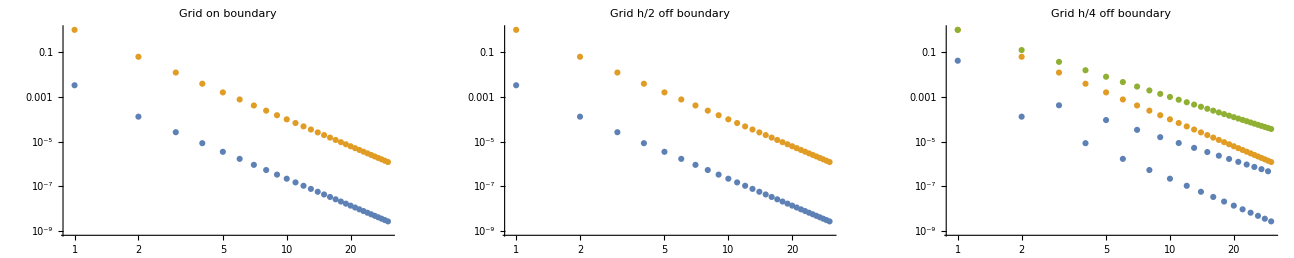

```mathematica
Show[
GraphicsGrid[
{
{ListLogLogPlot[
{Table[Abs[Re[f2hatθ[k]]] /. g1-> 1 /. g0-> 0.9 /. g2-> 1.2 /. x0-> 0.6 /. x2-> 0 /. θ->0 /. n-> 4,{k,1,30}],
Table[1/k^4,{k,1,30}]},PlotLabel->"Grid on boundary"],
ListLogLogPlot[
{Table[Abs[Re[f2hatθ[k]]] /. g1-> 1 /. g0-> 0.9 /. g2-> 1.2 /. x0-> 0.6 /. x2-> 0 /. θ->0.5 /. n-> 4,{k,1,30}],
Table[1/k^4,{k,1,30}]},PlotLabel->"Grid h/2 off boundary"],
ListLogLogPlot[
{Table[Abs[Re[f2hatθ[k]]] /. g1-> 1 /. g0-> 0.9 /. g2-> 1.2 /. x0-> 0.6 /. x2-> 0 /. θ->0.25 /. n-> 4,{k,1,30}],
Table[1/k^4,{k,1,30}],
Table[1/k^3,{k,1,30}]},PlotLabel->"Grid h/4 off boundary"]
}
}
]
]
```

### Final approximation comparison

Approximation

```mathematica
Manipulate[
ListLogLogPlot[{
Table[48(n^-a)^4 n(g2-x2)(g0-x0)PDF[NormalDistribution[0,1/(√n)],g1 -x0]PDF[NormalDistribution[0,1/(√n)],g1 -x2],{n,1,nmax}],
Table[
Abs[Re[1/(2 π)n ((ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π)/(2 √n)-(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π)/(2 √n)-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π)/(2 √n)+(ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π)/(2 √n)-(ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)])/(2 √n)-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)])/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)])/(2 √n)+(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)])/(2 √n))]]/.s-> k n^a /. θ-> 0,{n,1,nmax}],
Table[Abs[1/(2 π)n ((ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π)/(2 √n)-(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π)/(2 √n)-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π)/(2 √n)+(ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π)/(2 √n)-(ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)])/(2 √n)-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)])/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)])/(2 √n)+(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)])/(2 √n))]/.s-> k n^a /. θ-> 0,{n,1,nmax}]
}, PlotRange->Full,PlotLegends->{"EMSF","Real FT", "Abs FT"}],{{x0,0},-3,g0},{{x2,0},-3,g2},{{g0,0.6},0.5,3},{g1,0.5,3},{g2,0.5,3},{{k,1},1,20,1},{{a,0.75},0.5,1},{nmax,30,100}]
```